```mathematica
Table[PartitionTypeFormula[allGraphs5[k,"graph"]],{k,allGraphs5NullAtomKeys}]//Tally//Sort
```

{{p1,1},{p1x1+p2,15},{p1x1x1+3 p2x1+p3,25},{p1x1x1x1+6 p2x1x1+3 p2x2+4 p3x1+p4,10},{p1x1x1x1x1+10 p2x1x1x1+15 p2x2x1+10 p3x1x1+10 p3x2+5 p4x1+p5,1}}

```mathematica
Table[PartitionTypeFormula[allGraphs5[k,"graph"]],{k,allGraphs5GeneratorAtomKeys}]//Tally//Sort
```

{{p1x1x1x1x1,1},{p1x1x1x1x1+p2x1x1x1,10},{p1x1x1x1x1+2 p2x1x1x1+p2x2x1,15},{p1x1x1x1x1+3 p2x1x1x1+p3x1x1,10},{p1x1x1x1x1+4 p2x1x1x1+3 p2x2x1+p3x1x1+p3x2,10},{p1x1x1x1x1+6 p2x1x1x1+3 p2x2x1+4 p3x1x1+p4x1,5},{p1x1x1x1x1+10 p2x1x1x1+15 p2x2x1+10 p3x1x1+10 p3x2+5 p4x1+p5,1}}

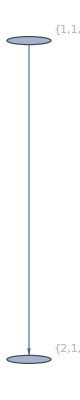
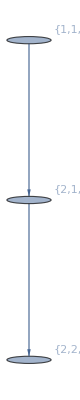
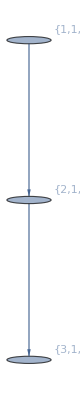
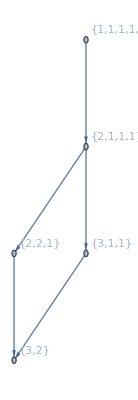
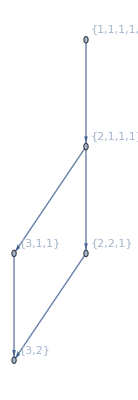
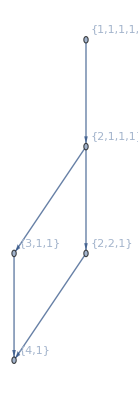
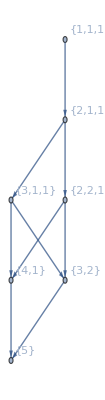
{{-Graphics-,1},{-Graphics-,10},{-Graphics-,15},{-Graphics-,10},{-Graphics-,6},{-Graphics-,4},{-Graphics-,5},{-Graphics-,1}}

```mathematica
Table[GraphLattice[allGraphs5[k,"graph"]],{k,allGraphs5GeneratorAtomKeys}]//Tally//Sort
```

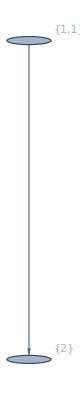
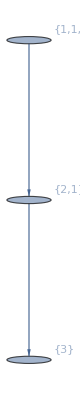
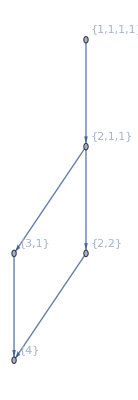
{{-Graphics-,1},{-Graphics-,15},{-Graphics-,25},{-Graphics-,10},{-Graphics-,1}}

```mathematica
Table[GraphLattice[allGraphs5[k,"graph"]],{k,allGraphs5NullAtomKeys}]//Tally//Sort
```

```mathematica
Select[Range[100],VertexCount[ReadGrof[#]]==6&]
```

{3,4}

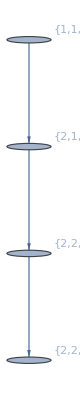
{{-Graphics-,1},{-Graphics-,1}}

```mathematica
Table[GraphLattice[ReadGrof[k]],{k,Select[Range[100],VertexCount[ReadGrof[#]]==6&]}]//Tally//Sort
```

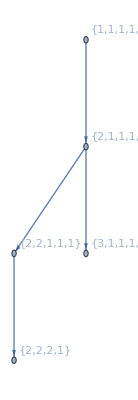
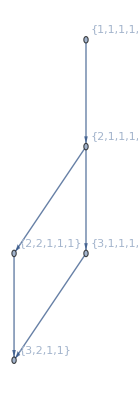
{{-Graphics-,3},{-Graphics-,1},{-Graphics-,1}}

```mathematica
Table[GraphLattice[ReadGrof[k]],{k,Select[Range[100],VertexCount[ReadGrof[#]]==7&]}]//Tally//Sort
```

```mathematica
Select[Range[100],VertexCount[ReadGrof[#]]==9&]
```

{24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73}

```mathematica
PartitionTypeLattice2[g_]:=With[{p=PartitionTypeLattice[g]},]
```

```mathematica
Table[PartitionTypeFormula[ReadGrof[k]],{k,Select[Range[100],VertexCount[ReadGrof[#]]==6&]}]//Tally//Sort
```

{{p1x1x1x1x1x1+3 p2x1x1x1x1+p2x2x1x1,1},{p1x1x1x1x1x1+3 p2x1x1x1x1+3 p2x2x1x1+p2x2x2,1}}

```mathematica
Table[PartitionTypeFormula[ReadGrof[k]],{k,Select[Range[100],VertexCount[ReadGrof[#]]==8&]}]//Tally//Sort
```

{{p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+25 p2x2x1x1x1x1+15 p2x2x2x1x1+p2x2x2x2,1},{p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+23 p2x2x1x1x1x1+12 p2x2x2x1x1+2 p3x1x1x1x1x1+3 p3x2x1x1x1+p2x2x2x2,1},{p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+21 p2x2x1x1x1x1+10 p2x2x2x1x1+4 p3x1x1x1x1x1+4 p3x2x1x1x1+p4x1x1x1x1+p2x2x2x2,1},{p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+29 p2x2x1x1x1x1+26 p2x2x2x1x1+3 p2x2x2x2,1},{p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+27 p2x2x1x1x1x1+22 p2x2x2x1x1+4 p2x2x2x2,1},{p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+24 p2x2x1x1x1x1+12 p2x2x2x1x1+p3x1x1x1x1x1+3 p3x2x1x1x1+p3x2x2x1,1},{p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+23 p2x2x1x1x1x1+10 p2x2x2x1x1+2 p3x1x1x1x1x1+5 p3x2x1x1x1+p3x2x2x1,1},{p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+22 p2x2x1x1x1x1+9 p2x2x2x1x1+3 p3x1x1x1x1x1+6 p3x2x1x1x1+p3x2x2x1,1},{p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+26 p2x2x1x1x1x1+20 p2x2x2x1x1+p3x1x1x1x1x1+2 p3x2x1x1x1+3 p2x2x2x2+p3x2x2x1,1},{p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+25 p2x2x1x1x1x1+18 p2x2x2x1x1+2 p3x1x1x1x1x1+4 p3x2x1x1x1+2 p2x2x2x2+2 p3x2x2x1,1},{p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+27 p2x2x1x1x1x1+22 p2x2x2x1x1+p3x1x1x1x1x1+3 p3x2x1x1x1+3 p2x2x2x2+2 p3x2x2x1,1},{p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+26 p2x2x1x1x1x1+18 p2x2x2x1x1+p3x1x1x1x1x1+4 p3x2x1x1x1+p2x2x2x2+3 p3x2x2x1,1},{p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+21 p2x2x1x1x1x1+5 p2x2x2x1x1+4 p3x1x1x1x1x1+10 p3x2x1x1x1+p3x3x1x1,1},{p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+27 p2x2x1x1x1x1+22 p2x2x2x1x1+2 p3x1x1x1x1x1+8 p3x2x1x1x1+4 p2x2x2x2+6 p3x2x2x1+p3x3x1x1+p3x3x2,1}}

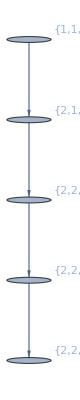
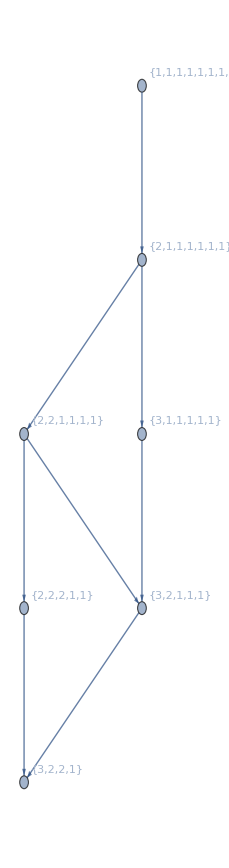
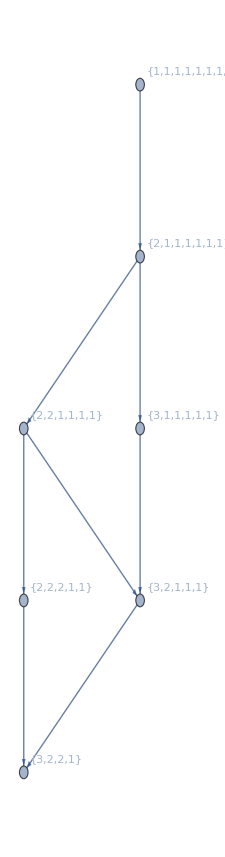
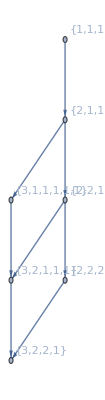
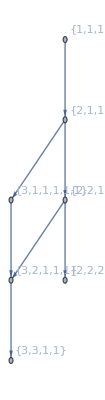
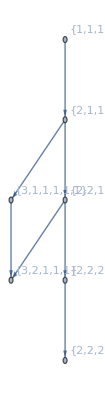
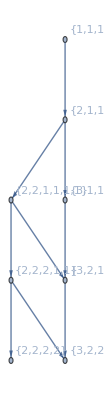
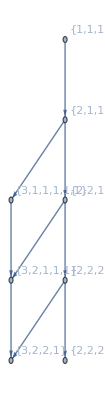
{{-Graphics-,3},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,2},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1}}

```mathematica
Table[GraphLattice[ReadGrof[k]],{k,Select[Range[100],VertexCount[ReadGrof[#]]==8&]}]//Tally//Sort
```

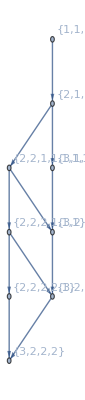
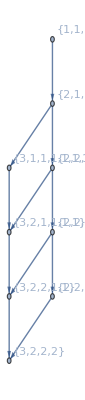
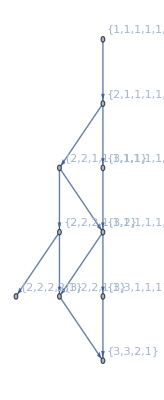
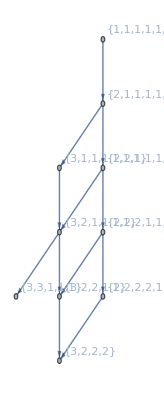
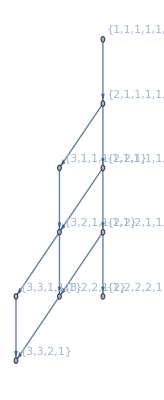
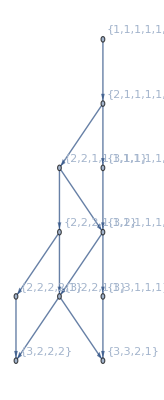
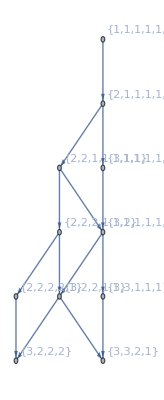
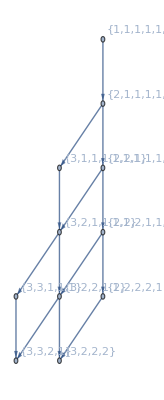
{{-Graphics-,8},{-Graphics-,4},{-Graphics-,2},{-Graphics-,2},{-Graphics-,6},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,2},{-Graphics-,1},{-Graphics-,4},{-Graphics-,1},{-Graphics-,1},{-Graphics-,4},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,2},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1}}

```mathematica
Table[GraphLattice[ReadGrof[k]],{k,Select[Range[100],VertexCount[ReadGrof[#]]==9&]}]//Tally//Sort
```